## 0.-Definiciones previas (copia todas las que necesites de ficheros de clase y si quieres definir alguna nueva)

Ejes coordenados

```mathematica
(*ejes*)ejes:=Graphics3D[{Red,Dashed,Arrow[{{-1,0,0},{2.5,0,0}}],Blue,Arrow[{{0,-1,0},{0,2.5,0}}],Yellow,Arrow[{{0,0,-1},{0,0,2.5}}]}]
B[n_,i_,t_]:=Binomial[n,i]*tt^i*(1-tt)^(n-i)/.tt->t (*Polinomios de Bernstein*)
B[n_,i_][t_]:=Binomial[n,i]*tt^i*(1-tt)^(n-i)/.tt->t
CurvaBezier[poligono_][t_]:=Sum[B[Length[poligono]-1,i,t]*poligono[[i+1]],{i,0,Length[poligono]-1}]//ExpandAll (*Curva de Bezier*)

M[n_][valort_,puntos_] :=Table[Table[B[n, i, valort[[j + 1]]],{i, 0,n}],  {j, 0, Length[puntos]-1}](*Matriz de Ajuste*)

(*n es el grado de la curva de Bézier (n+1 puntos de control)*)
A[n_][valort_,puntos_]:=Inverse[Transpose[M[n][valort,puntos]].M[n][valort,puntos]].Transpose[M[n][valort,puntos]]
approx[puntos_,valort_,n_]:=A[n][valort,puntos].puntos(*//Chop*) (*Cálculo de los puntos de control*)


Dibuja[poligono_]:=Show[Graphics[Line[poligono]],Graphics[Table[{Red,PointSize[Large],Point[poligono[[i+1]]]},{i,0,Length[poligono]-1}]],
ParametricPlot[CurvaBezier[poligono][t],{t,0,1},PlotStyle->Blue]]
```

```mathematica
supBezier[red_][u_,v_]:=Sum[B[Length[red]-1,i,u]*B[Length[red[[1]]]-1,j,v]*red[[i+1,j+1]],{i,0,Length[red]-1},{j,0,Length[red[[1]]]-1}]//Simplify//ExpandAll
```

```mathematica
supBezier2[red_][u_,v_,a_,b_,c_,d_]:=Sum[B[Length[red]-1,i][(u-a)/(b-a)]*B[Length[red[[1]]]-1,j][(v-c)/(d-c)]*red[[i+1,j+1]],{i,0,Length[red]-1},{j,0,Length[red[[1]]]-1}]//Simplify//ExpandAll (*nuestro rectángulo de parametrización es [0,π/2]×[0,2]*)
```

```mathematica
(* Matriz del cambio de base {polinomios de Berstein}  a la de potencias  {1,t,t^2,t^3,...,t^n} *)
MC[n_]:=Table[CoefficientList[B[n,i,t],t],{i,0,n}]
```

```mathematica
coef[poli_,n_,t_]:=If[Length[CoefficientList[poli,t]]-1>n,"No se puede, grado base Bernstein demasiado bajo" ,Join[CoefficientList[poli,t],Table[0,{i,1,n+1-Length[CoefficientList[poli,t]]}]].Inverse[MC[n]]]
```

```mathematica
denoSup[sup_][u_,v_]:=PolynomialLCM[Denominator[sup[u,v]][[1]],Denominator[sup[u,v]][[2]],Denominator[sup[u,v]][[3]]]//Simplify;
numSup[sup_][u_,v_]:=denoSup[sup][u,v]*sup[u,v]//Simplify
```

```mathematica
CurvaBezierRacional[poligono_,pesos_][t_]:=
Sum[B[Length[poligono]-1,i,t]*poligono[[i+1]]*pesos[[i+1]],{i,0,Length[poligono]-1}]/
Sum[B[Length[poligono]-1,i,t]*pesos[[i+1]],{i,0,Length[poligono]-1}]//Simplify
```

```mathematica
supBezRac[red_,pesos_][u_,v_]:=Sum[pesos[[i+1,j+1]]*red[[i+1,j+1]]B[Length[red]-1,i][u]B[Length[red[[1]]]-1,j][v],{i,0,Length[red]-1},{j,0,Length[red[[1]]]-1}]/Sum[pesos[[i+1,j+1]]B[Length[red]-1,i][u]B[Length[red[[1]]]-1,j][v],{i,0,Length[red]-1},{j,0,Length[red[[1]]]-1}]//Simplify
```

```mathematica
mCoef[sup_][u_,v_,m_,n_]:=Table[Coefficient[Coefficient[sup[u,v],u,i],v,j],{i,0,m},{j,0,n}]
mUsBer[n_]:=Inverse[Table[CoefficientList[B[n,i][t],t],{i,0,n}]]
```

```mathematica
pesosSup[sup_,m_,n_]:=If[Length[CoefficientList[denoSup[sup][u,v],u]]-1>m ||Length[CoefficientList[denoSup[sup][u,v],v]]-1>n ,"No se puede, grado base Bernstein demasiado bajo" ,Transpose[mUsBer[m]].Table[Table[Sum[mCoef[denoSup[sup]][u,v,m,n][[i+1,j+1]]mUsBer[n][[j+1,k+1]],{j,0,n}],{k,0,n}],{i,0,m}]]//Simplify
```

```mathematica
(*Puntos de control de la superfície racional de grados m y n *)puntContRac[sup_,m_,n_]:=If[Max[Table[Length[CoefficientList[numSup[sup][u,v][[i]],u]],{i,1,3}]]-1>m ||Max[Table[Length[CoefficientList[numSup[sup][u,v][[i]],v]],{i,1,3}]]-1>n ,"No se puede, grado base Bernstein demasiado bajo" ,Transpose[mUsBer[m]].Table[Table[Sum[mCoef[numSup[sup]][u,v,m,n][[i+1,j+1]]mUsBer[n][[j+1,k+1]],{j,0,n}],{k,0,n}],{i,0,m}]]/pesosSup[sup,m,n]//Simplify
```

```mathematica
red[n_]:=Map[ToExpression[StringJoin["P",#]]&,
Apply[StringJoin,Map[ToString,Table[{i,j},{i,0,n},{j,0,n}],{-1}],{2}],{-1}]
```

```mathematica
condArmo[sup_][u_,v_]:=Flatten[CoefficientList[CoefficientList[D[sup[u,v],{u,2}]+D[sup[u,v],{v,2}]//Simplify,u],v]]
```

# Gráficas

```mathematica
data = Import["D:/Desktop/Estudios/UNIVERSIDAD/Investmat/TFM/codigos_final/8_histogramas2019.csv"]
```

{1}
 |  |  |  |

```mathematica
data[[;;,2]]
```

{290195,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,68.,20.,10.,7.,5.,8.,7.,3.,7.,1.,7.,14.,15.,5.,20.,41.,22.,16.,11.,16.,9.,10.,22.,19.,51.,19.,14.,5.,57.,12.,5.,1.,5.,4.,2.,2.,1.,2.,10.,32.,3.,1.,1.,1.,0.,1.}

```mathematica
datatodeal = data[[;;,2]][[2;;]];
datatodeal2 = data[[;;,3]][[2;;]];
```

```mathematica
datatodeal = datatodeal/Total[datatodeal]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00168067,0.,0.,0.00168067,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.00168067,0.,0.,0.114286,0.0336134,0.0168067,0.0117647,0.00840336,0.0134454,0.0117647,0.00504202,0.0117647,0.00168067,0.0117647,0.0235294,0.0252101,0.00840336,0.0336134,0.0689076,0.0369748,0.0268908,0.0184874,0.0268908,0.0151261,0.0168067,0.0369748,0.0319328,0.0857143,0.0319328,0.0235294,0.00840336,0.0957983,0.0201681,0.00840336,0.00168067,0.00840336,0.00672269,0.00336134,0.00336134,0.00168067,0.00336134,0.0168067,0.0537815,0.00504202,0.00168067,0.00168067,0.00168067,0.,0.00168067}

```mathematica
tiempos = Subdivide[Length[datatodeal]-1] ;
```

```mathematica
puntosCurva = Table[{i-1,datatodeal[[i]]}, {i,Length[datatodeal]}];
```

```mathematica
puntosCurva2 = Table[{i-1,datatodeal2[[i]]}, {i,Length[datatodeal2]}];
```

```mathematica
puntosControl=N[approx[puntosCurva,tiempos,7]](*Puntos de control*)
puntosControl2=N[approx[puntosCurva2,tiempos,7]];
```

{{8.88178×10^-16,0.00220383},{10.1429,-0.0133306},{20.2857,0.0198975},{30.4286,-0.00344148},{40.5714,0.0318165},{50.7143,0.0831891},{60.8571,-0.0129578},{71.,0.00486957}}

```mathematica
curva[t_]:=CurvaBezier[puntosControl][t] (*parametrización del primer cuarto de circunferencia*)
curva2[t_]:=CurvaBezier[puntosControl2][t] (*parametrización del primer cuarto de circunferencia*)
```

```mathematica
puntosControlDibujo=Table[{PointSize->Large,Cyan,Point[puntosControl[[i]]]},{i,Length[puntosControl]}];
puntosControlDibujo2=Table[{PointSize->Large,Cyan,Point[puntosControl2[[i]]]},{i,Length[puntosControl2]}];
```

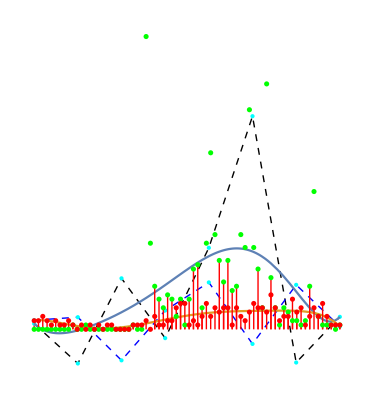

```mathematica
Show[
Graphics[{{Dashed,Line[puntosControl]},Blue,PointSize[Medium],puntosControlDibujo,{Dashed,Line[puntosControl2]},Blue,PointSize[Medium],Blue,puntosControlDibujo2}],
ParametricPlot[{curva[t],curva2[t]},{t,0,1}],
ListPlot[{puntosCurva,puntosCurva2},PlotStyle->{Green,Red} ,Filling->Axis, FillingStyle->{Green,Red} ]

]
```

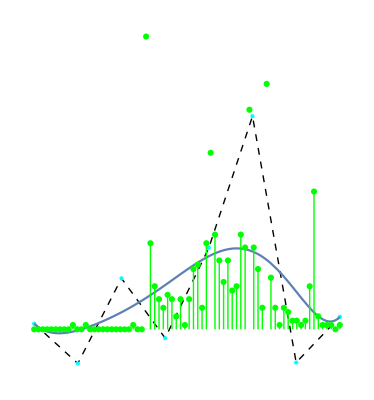

```mathematica
Show[
Graphics[{{Dashed,Line[puntosControl]},Blue,PointSize[Medium],puntosControlDibujo}],
ParametricPlot[curva[t],{t,0,1}],
ListPlot[puntosCurva,PlotStyle->Green ,Filling->Axis, FillingStyle->Green ]

]
```

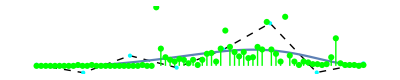

```mathematica
Show[
Graphics[{{Dashed,Line[puntosControl]},Blue,PointSize[Medium],puntosControlDibujo}],
ParametricPlot[curva[t],{t,0,1}],
ListPlot[puntosCurva,PlotStyle->Green ,Filling->Axis, FillingStyle->Green ]

]
```

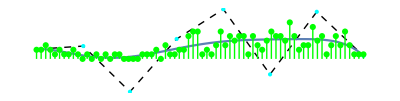

```mathematica
Show[
Graphics[{{Dashed,Line[puntosControl2]},Blue,PointSize[Medium],puntosControlDibujo2}],
ParametricPlot[curva2[t],{t,0,1}],
ListPlot[puntosCurva2,PlotStyle->Green ,Filling->Axis, FillingStyle->Green ]

]
```